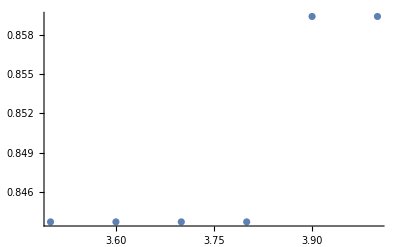

```mathematica
a={{3.5,(65-10-1)/64}, {3.6,(65-10-1)/64},{3.7,(65-10-1)/64},{3.8,(65-10-1)/64}, {3.9,(65-9-1)/64},{4.0,(65-9-1)/64}};
ListPlot[a]
```

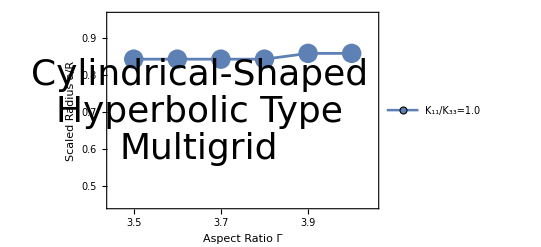

```mathematica
ListPlot[{a},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.5,0.6,0.7,0.8,0.9},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.45,4.05},{0.45,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.65,0.8}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.65,0.7}],Text[Style["Multigrid",Directive[Black,36]],{3.65,0.6}]}]
```

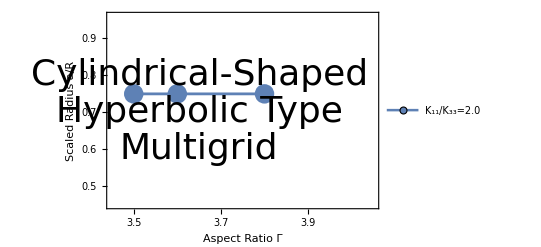

```mathematica
a2={{3.5,(65-16-1)/64}, {3.6,(65-16-1)/64},{3.8,(65-16-1)/64}};
ListPlot[{a2},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.5,0.6,0.7,0.8,0.9},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.45,4.05},{0.45,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=2.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.65,0.8}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.65,0.7}],Text[Style["Multigrid",Directive[Black,36]],{3.65,0.6}]}]
```

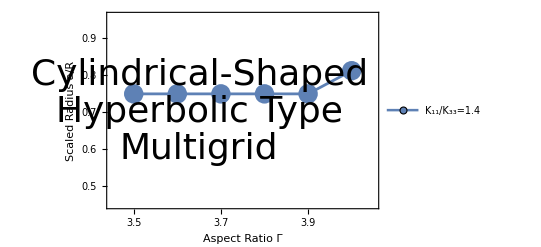

```mathematica
a3={{3.5,(65-16-1)/64}, {3.6,(65-16-1)/64},{3.7,(65-16-1)/64},{3.8,(65-16-1)/64}, {3.9,(65-16-1)/64},{4.0,(65-12-1)/64}};
ListPlot[{a3},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.5,0.6,0.7,0.8,0.9},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.45,4.05},{0.45,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.65,0.8}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.65,0.7}],Text[Style["Multigrid",Directive[Black,36]],{3.65,0.6}]}]
```

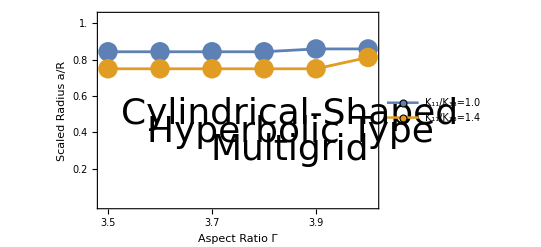

```mathematica
ListPlot[{a,a3},PlotStyle->{Thickness[0.005],Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=1.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.85,0.5}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.85,0.4}],Text[Style["Multigrid",Directive[Black,36]],{3.85,0.3}]}]
```

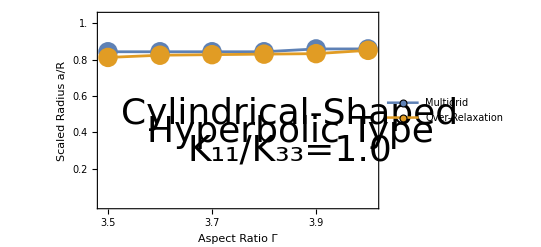

```mathematica
aa={{3.5,91/(3.5×32)}, {3.6,95/(3.6×32)},{3.7,98/(3.7×32)},{3.8,101/(3.8×32)}, {3.9,104/(3.9×32)},{4.0,109/(4×32)}};
ListPlot[{a,aa},PlotStyle->{Thickness[0.005],Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Multigrid","Over-Relaxation"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.85,0.5}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.85,0.4}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{3.85,0.3}]}]
```

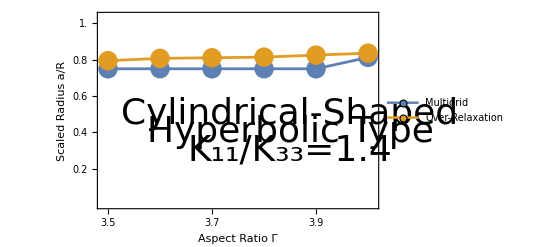

```mathematica
aa3={{3.5,89/(3.5×32)}, {3.6,93/(3.6×32)},{3.7,96/(3.7×32)},{3.8,99/(3.8×32)}, {3.9,103/(3.9×32)},{4.0,107/(4×32)}};
ListPlot[{a3,aa3},PlotStyle->{Thickness[0.005],Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Multigrid","Over-Relaxation"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.85,0.5}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.85,0.4}],Text[Style["K_11/K_33=1.4",Directive[Black,36]],{3.85,0.3}]}]
```

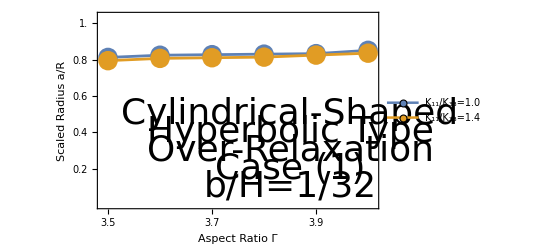

```mathematica
ListPlot[{aa,aa3},PlotStyle->{Thickness[0.005],Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=1.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.85,0.5}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.85,0.4}],Text[Style["Over-Relaxation",Directive[Black,36]],{3.85,0.3}],Text[Style["Case (1)",Directive[Black,36]],{3.85,0.2}],Text[Style["b/H=1/32",Directive[Black,36]],{3.85,0.1}]}]
```

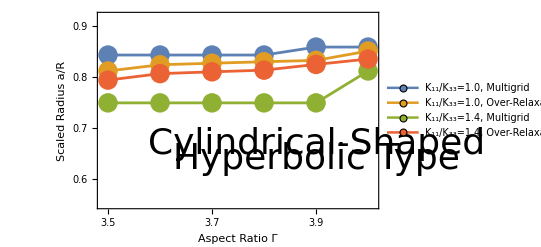

```mathematica
ListPlot[{a,aa,a3,aa3},PlotStyle->{Thickness[0.005],Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.6,0.7,0.8,0.9},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{0.55,0.92}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0, Multigrid","K_11/K_33=1.0, Over-Relaxation","K_11/K_33=1.4, Multigrid","K_11/K_33=1.4, Over-Relaxation"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.9,0.67}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.9,0.64}]}]
```